```mathematica
Integrate[(2*x+1)*Exp[-u*x(x+1)],{x,0,Infinity}]
```

ConditionalExpression[1/u, Re[u]>0]

```mathematica
M=(2*I*t+1)*Exp[-u*I*t(I*t+1)]-(2*-I*t+1)*Exp[-u*-I*t(-I*t+1)]//FullSimplify
```

2 ⅈ ⅇ^(t^2 u) (2 t Cos[t u]-Sin[t u])

```mathematica
K=M/(Exp[2*Pi*t]-1)//FullSimplify
```

ⅈ ⅇ^(t^2 u) (-1+Coth[π t]) (2 t Cos[t u]-Sin[t u])

```mathematica
Series[K,{u,0,1}]//FullSimplify
```

2 ⅈ t (-1+Coth[π t])+ⅈ t (-1+2 t^2) (-1+Coth[π t]) u+O[u]^2

```mathematica
I*Integrate[2 ⅈ t (-1+Coth[π t]),{t,0,Infinity}]
```

-1/6

```mathematica
I*Integrate[ⅈ t (-1+2 t^2) (-1+Coth[π t]),{t,0,Infinity}]
```

1/15

```mathematica
Z=1/u+1/3+u/15/.{u->hbar^2/(2*II*kB*T)}/.{kB*T->1/b}/.{1/(kB*T)->b}
```

1/3+(b hbar^2)/(30 II)+(2 II)/(b hbar^2)

```mathematica
En=D[-Log[Z],b]//FullSimplify
```

1/b-(2 (b hbar^4+5 hbar^2 II))/(b^2 hbar^4+10 b hbar^2 II+60 II^2)

```mathematica
Limit[(-2 (b hbar^4+5 hbar^2 II))/(b^2 hbar^4+10 b hbar^2 II+60 II^2),b->0]
```

-hbar^2/(6 II)

```mathematica
E1=-(2 (b hbar^4+5 hbar^2 II))/(b^2 hbar^4+10 b hbar^2 II+60 II^2)/.{b->1/(kB*T)}//FullSimplify
```

-(2 kB T (hbar^4+5 hbar^2 II kB T))/(hbar^4+10 hbar^2 II kB T+60 II^2 kB^2 T^2)

```mathematica
D[E1,T]//FullSimplify//TeXForm
```

-\frac{2 \text{hbar}^4 \text{kB} \left(\text{hbar}^4+10 \text{hbar}^2 \text{II}
   \text{kB} T-10 \text{II}^2 \text{kB}^2 T^2\right)}{\left(\text{hbar}^4+10
   \text{hbar}^2 \text{II} \text{kB} T+60 \text{II}^2 \text{kB}^2 T^2\right)^2}

```mathematica
f=Series[Log[(1/2)*Csch[β*h*ω/2]],{β,0,2}]
```

Log[1/(h β ω)]-1/24 (h^2 ω^2) β^2+O[β]^3

```mathematica
D[-f,β]/.{β->1/(k*T)}//FullSimplify
```

SeriesData::sdatv: First argument 1/(k T) is not a valid variable.

1/(1/(k T))+(h^2 ω^2)/(12 k T)+O[1/(k T)]^2

```mathematica
f=f /.{β->1/(k*T)}
```

SeriesData::sdatv: First argument 1/(k T) is not a valid variable.

Log[(k T)/(h ω)]-1/24 (h^2 ω^2) (1/(k T))^2+O[1/(k T)]^3

```mathematica
Z=V^M/(Factorial[M]*L^(3*M))*Exp[β*b*M^2/(2*V) - β*c*M^3/(6*V^2)];
```

```mathematica
F=-k*T*Log[Z];
```

```mathematica
P=-D[F,V]/.{β->(1/(k*T))}//Expand
```

(c M^3)/(3 V^3)-(b M^2)/(2 V^2)+(k M T)/V

```mathematica
P=P/.{M/V->n,M^2/V^2->n^2,M^3/V^3->n^3}
```

-(b n^2)/2+(c n^3)/3+k n T

```mathematica
eqn1=D[P,n]
```

-b n+c n^2+k T

```mathematica
eqn2=D[P,{n,2}]
```

-b+2 c n

```mathematica
Solve[{eqn1==0,eqn2==0},{n,T}]
```

{{n→b/(2 c),T→b^2/(4 c k)}}

```mathematica
nc=b/(2 c);
```

```mathematica
Tc=b^2/(4 c k);
```

```mathematica
Pc=-(b nc^2)/2+(c nc^3)/3+k*nc*Tc
```

b^3/(24 c^2)

```mathematica
R=k*Tc*nc/Pc
```

3

```mathematica
D[P,n]
```

-b n+c n^2+k T

```mathematica
K=-1/(n*D[P,n])
```

-1/(n (-b n+c n^2+k T))

```mathematica
Kc=K/.{n->b/(2 c)}//FullSimplify
```

(8 c^2)/(b^3-4 b c k T)

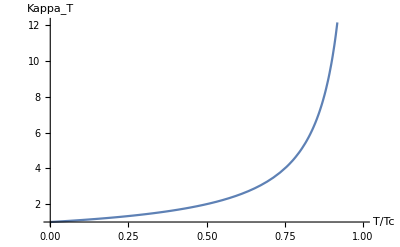

```mathematica
Plot[1/(1-x),{x,0,1},AxesLabel->{"T/Tc","Kappa_T"}]
```